```mathematica
Clear[ζ,ω0]
sol=Simplify[DSolve[{x''[t]+x'[t]2 ω0 ζ+ω0^2 x[t]==0,x[0]==1,x'[0]==0},x,t]];
Simplify[x[t]/.sol,{ω0>0,ζ>0,t>0}]
```

{1/(2 (-1+ζ^2))ⅇ^(-t (ζ+√(-1+ζ^2)) ω0) (-1+ζ^2-ζ √(-1+ζ^2)+ⅇ^(2 t √(-1+ζ^2) ω0) (-1+ζ^2+ζ √(-1+ζ^2)))}

```mathematica
f[x_]=(a x^3+b x^2+c x +d)/ei;
sol=Solve[{(D[f[x],{x,1}]/.x->l)==Sin[θ2],(D[f[x],{x,1}]/.x->0)==Sin[θ1 ],
(D[f[x],{x,1}]/.x->0)==w0,(D[f[x],{x,3}]/.x->l)==w1},{a,b,c,d}];
(* Torque *)
Simplify[-D[f[x] e l^4,{x,2}]/.sol[[1]]/.x->{0,l}]
(* shear force *)
Simplify[-D[f[x] e l^4,{x,3}]/.sol[[1]]/.x->{0,l}]
```

{-(2 b e l^4)/ei,-(2 e l^4 (b+3 a l))/ei}/.{}⟦1⟧

-(6 a e l^4)/ei/.{}⟦1⟧

```mathematica
({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}}).({{x}, {y}})/.θ->π/2
```

{{-y},{x}}

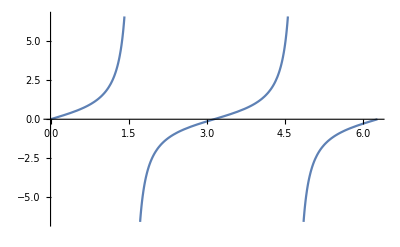

```mathematica
Plot[Tan[θ+π],{θ,0,2π}]
```

```mathematica
X1  = {x1[t],y1[t]};
X2 = {x2[t],y2[t]};
eq={D[X1,{t,2}]==((-(X1-X2))/((X1-X2).(X1-X2))((X1-X2).(X1-X2)-x0))κ,D[X2,{t,2}]==((X1-X2)/((X1-X2).(X1-X2))((X1-X2).(X1-X2)-x0))κ,
(X1/.t->0)=={-1,0},(X2/.t->0)=={1,0},
(D[X1,{t,1}]/.t->0)=={0,1},(D[X2,{t,1}]/.t->0)=={0,-1}}
sol=Simplify[DSolve[eq,{x1,y1,x2,y2},t]]/.{κ->(2π)^2,x0->2}
ParametricPlot[{{x1[t],y1[t]},{x2[t],y2[t]}}/.sol,{t,0,10}]
```

{{x1''[t],y1''[t]}=={-(κ (x1[t]-x2[t]) (-x0+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2),-(κ (-x0+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2) (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)},{x2''[t],y2''[t]}=={(κ (x1[t]-x2[t]) (-x0+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2),(κ (-x0+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2) (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)},{x1[0],y1[0]}=={-1,0},{x2[0],y2[0]}=={1,0},{x1'[0],y1'[0]}=={0,1},{x2'[0],y2'[0]}=={0,-1}}

DSolve[{{x1''[t],y1''[t]}=={-(4 π^2 (x1[t]-x2[t]) (-2+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2),-(4 π^2 (-2+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2) (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)},{x2''[t],y2''[t]}=={(4 π^2 (x1[t]-x2[t]) (-2+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2),(4 π^2 (-2+(x1[t]-x2[t])^2+(y1[t]-y2[t])^2) (y1[t]-y2[t]))/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)},{x1[0],y1[0]}=={-1,0},{x2[0],y2[0]}=={1,0},{x1'[0],y1'[0]}=={0,1},{x2'[0],y2'[0]}=={0,-1}},{x1,y1,x2,y2},t]

-Graphics-